# Lyapunov Exponents

## Introduction

This code follows the "deviation vector method" of calculating the largest Lyapunov exponent for unconstrained systems of differential equations, as outlined in the paper at http://arxiv.org/abs/physics/0303077. It is written for the Lorenz equations, but simple modifications will allow it to work for other systems, like the driven pendulum.

## The Code

Constants

First, declare all the constants.

```mathematica
s=10;
b=8/3;
r=38;
T1=10;
T2 = 15;
minT = 13;
maxT = 15;
time = 0;
ratio = 0;
ratiolist = {};

maxdr = 10^(-4);
dr = 10^(-8);
x1=1.;
x2 = x1 + dr;
y1=1.;
y2 = y1 + dr;
z1=1.;
z2 = z1 + dr;
```

s, b, and r are the constants in the lorenz equations, dr is the difference in initial conditions, and the x, y, z values are the initial conditions for both trajectories. You can vary the value of x1, y1, z1, and you can try changing x2, y2, z2 so that they are not all shifted by the same amount. T1, T2, minT, and maxT are the lower and upper time bounds for the NDSolve commands and the second for loop; see the last code segment for an explanation of why they are used.

Initial solutions

Next, generate the first set of solutions:

```mathematica
solA=NDSolve[{x'[t] ==s(y[t]- x[t]),y'[t] ==r*x[t]-y[t]-x[t]*z[t],z'[t] == x[t]*y[t]- b*z[t],x[0]==x1,y[0]==y1,z[0]==z1},{x,y,z},{t,0,50} ,MaxStepFraction->1/100,MaxSteps->100000] ;

solB=NDSolve[{x'[t] ==s(y[t]- x[t]),y'[t] ==r*x[t]-y[t]- x[t]*z[t],z'[t] == x[t]*y[t]- b*z[t],x[0]==x2,y[0]==y2,z[0]==z2},{x,y,z},{t,0,50} ,MaxStepFraction->1/100,MaxSteps->100000] ;
```

Loops and calculating each deviation factor

Now use two for loops, one to specify the number of times to calculate and rescale the deviation vector, and the other to loop until the deviation vector reaches the given size. To determine the range of values that the second loop should evaluate the solutions at, it is necessary to determine at what values the deviation vector approaches the maximum (see below). This saves considerable computation time, since it is not until t approaches 10 that the deviation vector reaches the order of 10^-4. Once the deviation vector reaches the maximum size, the log of the deviation factor is recorded, as is the time. New solutions are then computed using the x,y,z values at which the deviation vector exceeded the maximum size as the new initial conditions. The initial deviation vector is added as it was above to the second set of initial conditions, the loop repeats.

```mathematica
For[n=0,n<100,n++,
For[t=minT,t<maxT,t = t+.0005,

delta=√(((x[t]/.solB)-(x[t]/.solA))^2+((y[t]/.solB)-(y[t]/.solA))^2+((z[t]/.solB)-(z[t]/.solA))^2);

If[
First[delta]>maxdr,
newstart = t;
time = time + t;
ratio = ratio +  Log[First[delta]/(3^(1/2)*dr)];
ratiolist = Append[ratiolist, {time,ratio}];
Break[];
]
];

x1=First[x[newstart]/.solA];
y1=First[y[newstart]/.solA];
z1=First[z[newstart]/.solA];
x2=x1+dr;
y2=y1+dr;
z2=z1+dr;
Clear[solA,solB,x,y,z,t];

solA=NDSolve[{x'[t]==s (y[t]-x[t]),y'[t]==r x[t]-y[t]-x[t] z[t],z'[t]==x[t] y[t]-b z[t],x[0]==x1,y[0]==y1,z[0]==z1},{x,y,z},{t,T1,T2},MaxStepFraction->1/100,MaxSteps->100000];

solB=NDSolve[{x'[t]==s (y[t]-x[t]),y'[t]==r x[t]-y[t]-x[t] z[t],z'[t]==x[t] y[t]-b z[t],x[0]==x2,y[0]==y2,z[0]==z2},{x,y,z},{t,T1,T2},MaxStepFraction->1/100,MaxSteps->100000];
]
```

Determining the exponent

Now, plot the deviation factor against time, and find the slope, which will be equal to the Lyapunov exponent.

1.08321

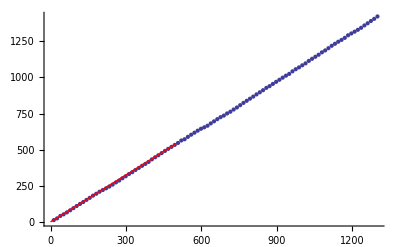

```mathematica
line = Fit[ratiolist,x,x]/x
points = ListPlot[ratiolist, DisplayFunction->Identity];
curve = Plot[line*x,{x,0,500},PlotStyle->{Thick,Red}, DisplayFunction->Identity];
Show[points, curve, DisplayFunction->$DisplayFunction]
```

Determining the time range

To determine a good range for the NDSolve commands and the second loop - i.e., a range of time values in which the deviation vector reaches its maximum, use the following code. Make sure that solA and solB are the correct interpolating functions, i.e., solutions to the initial trajectories.

```mathematica
solA=NDSolve[{x'[t] ==s(y[t]- x[t]),y'[t] ==r*x[t]-y[t]-x[t]*z[t],z'[t] == x[t]*y[t]- b*z[t],x[0]==x1,y[0]==y1,z[0]==z1},{x,y,z},{t,0,50} ,MaxStepFraction->1/100,MaxSteps->100000] ;

solB=NDSolve[{x'[t] ==s(y[t]- x[t]),y'[t] ==r*x[t]-y[t]- x[t]*z[t],z'[t] == x[t]*y[t]- b*z[t],x[0]==x2,y[0]==y2,z[0]==z2},{x,y,z},{t,0,50} ,MaxStepFraction->1/100,MaxSteps->100000] ;
```

```mathematica
solB
```

{{x→InterpolatingFunction[{{0.,50.}},<>],y→InterpolatingFunction[{{0.,50.}},<>],z→InterpolatingFunction[{{0.,50.}},<>]}}

```mathematica
solA
```

{{x→InterpolatingFunction[{{0.,50.}},<>],y→InterpolatingFunction[{{0.,50.}},<>],z→InterpolatingFunction[{{0.,50.}},<>]}}

```mathematica
For[i=0,i<20,i = i+1,
delta = (((x[i] /. solB) - (x[i] /. solA))^2 + ((y[i] /. solB) - (y[i] /. solA))^2 + ((z[i] /. solB) - (z[i] /. solA))^2)^(1/2);
Print[{i, First[delta]}];
]
```

{0,1.73205×10^-8}

{1,2.75055×10^-8}

{2,3.9719×10^-8}

{3,5.36008×10^-8}

{4,2.81172×10^-7}

{5,3.34038×10^-7}

{6,0.000016904}

{7,1.08563×10^-6}

{8,1.8545×10^-6}

{9,0.0000366966}

{10,0.0000386876}

{11,0.0000625964}

{12,0.0000693292}

{13,0.000560251}

{14,0.000954509}

{15,0.00494038}

{16,0.0186601}

{17,0.013786}

{18,0.0562761}

{19,0.238657}

You can tell by inspection roughly where the deviation vector exceeds whatever maximum you have entered. It's a good idea to use a generous range, since the deviation of different trajectories might exceed the maximum at different values of t. It is found in practice that quite a narrow range suffices, since all of the trajectories are so similar. Once you know the range, you can limit both the second for loop  and the values of t in the NDSolve commands to this range to save time. This is the purpose of T1 and T2, and minT and maxT. The range for the loop is narrower than that for the NDSolve commands to avoid error messages.